```mathematica
α = ({{α1}, {α2}});
c0=({{c01}, {c02}});
c1=({{c11}, {c12}});
β1=({{β11}, {β12}});
β2=({{β21}, {β22}});
A0=({{A011, A012}, {A021, A022}}); (* A0=({{A011, A012, A013}, {A021, A022, A023}, {A031, A032, A033}}); *)
B0=({{B011, B012}, {B021, B022}}); (* Subscript[B, 0]=({{B011, B012, B013}, {B021, B022, B023}, {B031, B032, B033}}); *)
H0=({{H01}, {H02}});
VU=({{U}, {U}});
e = ({{1}, {1}});
```

```mathematica
K1=IdentityMatrix[2] - μ h A0 ;
MatrixForm[K1 ]
```

(1-A011 h μ | -A012 h μ
-A021 h μ | 1-A022 h μ)

```mathematica
K2 = VU + B0 . e  σ (σ I10)/h;
MatrixForm[K2]
```

(U+((B011+B012) I10 σ^2)/h
U+((B021+B022) I10 σ^2)/h)

```mathematica
H0= Inverse[K1].K2;
MatrixForm[H0]
```

(((1-A022 h μ) (U+((B011+B012) I10 σ^2)/h))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)+(A012 h μ (U+((B021+B022) I10 σ^2)/h))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)
(A021 h μ (U+((B011+B012) I10 σ^2)/h))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)+((1-A011 h μ) (U+((B021+B022) I10 σ^2)/h))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2))

```mathematica
U2= U+ μ h αᵀ.H0 + σ I1 Transpose[e].β1+ σ I10/h Transpose[e].β2;
U2 =U2[[1]][[1]];
U2
```

U+I1 (β11+β12) σ+(I10 (β21+β22) σ)/h+h μ (α1 (((1-A022 h μ) (U+((B011+B012) I10 σ^2)/h))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)+(A012 h μ (U+((B021+B022) I10 σ^2)/h))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2))+α2 ((A021 h μ (U+((B011+B012) I10 σ^2)/h))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)+((1-A011 h μ) (U+((B021+B022) I10 σ^2)/h))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)))

```mathematica
I10=1/2 h(W+Z/(√3)); 
I1= W;
```

```mathematica
U2Full = U2
```

U+W (β11+β12) σ+1/2 (W+Z/(√3)) (β21+β22) σ+h μ (α1 (((1-A022 h μ) (U+1/2 (B011+B012) (W+Z/(√3)) σ^2))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)+(A012 h μ (U+1/2 (B021+B022) (W+Z/(√3)) σ^2))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2))+α2 ((A021 h μ (U+1/2 (B011+B012) (W+Z/(√3)) σ^2))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)+((1-A011 h μ) (U+1/2 (B021+B022) (W+Z/(√3)) σ^2))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)))

```mathematica
U2Plugged = U2Full /.  {W -> 0,Z->0}
G = Coefficient[U2Plugged,U]
```

U+h μ (α2 ((A021 h U μ)/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)+(U (1-A011 h μ))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2))+α1 ((A012 h U μ)/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)+(U (1-A022 h μ))/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)))

1+(h α1 μ)/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)+(h α2 μ)/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)+(A012 h^2 α1 μ^2)/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)-(A022 h^2 α1 μ^2)/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)-(A011 h^2 α2 μ^2)/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)+(A021 h^2 α2 μ^2)/(1-A011 h μ-A022 h μ-A012 A021 h^2 μ^2+A011 A022 h^2 μ^2)

```mathematica
stableeq = FullSimplify[G/.  {μ -> z/h}]
```

(1+z (α1+A012 z (-A021+α1)-A022 (1+z α1)+α2+A021 z α2+A011 (-1+A022 z-z α2)))/(1-z (A022+A012 A021 z)+A011 z (-1+A022 z))

```mathematica
TeXForm[stableeq]
```

\frac{z (\text{A011} (\text{A022} z-\text{$\alpha $2} z-1)+\text{A012} z (\text{$\alpha $1}-\text{A021})+\text{A021} \text{$\alpha $2}
   z-\text{A022} (\text{$\alpha $1} z+1)+\text{$\alpha $1}+\text{$\alpha $2})+1}{\text{A011} z (\text{A022} z-1)-z (\text{A012}
   \text{A021} z+\text{A022})+1}

```mathematica
Solve[1+z (α1+A012 z (-A021+α1)-A022 (1+z α1)+α2+A021 z α2+A011 (-1+A022 z-z α2))==1-z (A022+A012 A021 z)+A011 z (-1+A022 z),z]
```

{{z→0},{z→(α1+α2)/(-A012 α1+A022 α1+A011 α2-A021 α2)}}

```mathematica
Transpose[α].A0.e
```

{{A011 α1+A012 α1+A021 α2+A022 α2}}

```mathematica
FullSimplify[1+z (α1+A012 z (-A021+α1)-A022 (1+z α1)+α2+A021 z α2+A011 (-1+A022 z-z α2))==1-z (A022+A012 A021 z)+A011 z (-1+A022 z) /. z-> 1]
```

α1+A012 α1+α2+A021 α2==A022 α1+A011 α2

```mathematica
FullSimplify[A012 α1+A021 α2-A022 α1+A011 α2]
```

A012 α1-A022 α1+(A011+A021) α2

```mathematica
FindInstance[{A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,A021+A022==1},{A011,A012,A021,A022,α1,α2},Reals]
```

{{A011→0,A012→0,A021→-1,A022→2,α1→1/2,α2→1/2}}

```mathematica
A0.e
```

{{A011+A012+A013},{A021+A022+A023},{A031+A032+A033}}

```mathematica
FindInstance[{A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,A011==0}/.{A021-> 1/2,A022->1/2},{A011,A012,α1,α2},Reals]
```

{}

```mathematica
FindInstance[{A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,A011==1/2}/.{A021-> 1/2,A022->1/2},{A011,A012,α1,α2},Reals]
```

{{A011→1/2,A012→0,α1→1,α2→0}}

```mathematica
FindInstance[{A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,A011==1/4,A012== -1/4}/.{A021-> 1/2,A022->5/12},{A011,A012,α1,α2},Reals]
```

{}

```mathematica
FindInstance[{A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠ 0}/.{A021-> 1/2,A022->1/2},{A011,A012,α1,α2},Reals]
```

{{A011→-1,A012→6/11,α1→11/32,α2→21/32}}

```mathematica
Det[({{A011, A012}, {A021, A022}})]
```

-A012 A021+A011 A022

```mathematica
B=({{α1, 0}, {0, α2}})
M = B.A0 + Transpose[A0].B - α.Transpose[α]
```

{{α1,0},{0,α2}}

{{2 A011 α1-α1^2,A012 α1+A021 α2-α1 α2},{A012 α1+A021 α2-α1 α2,2 A022 α2-α2^2}}

```mathematica
Eigenvalues[M]
```

{1/2 (2 A011 α1-α1^2+2 A022 α2-α2^2-√((-2 A011 α1+α1^2-2 A022 α2+α2^2)^2-4 (-A012^2 α1^2-2 A012 A021 α1 α2+4 A011 A022 α1 α2+2 A012 α1^2 α2-2 A022 α1^2 α2-A021^2 α2^2-2 A011 α1 α2^2+2 A021 α1 α2^2))),1/2 (2 A011 α1-α1^2+2 A022 α2-α2^2+√((-2 A011 α1+α1^2-2 A022 α2+α2^2)^2-4 (-A012^2 α1^2-2 A012 A021 α1 α2+4 A011 A022 α1 α2+2 A012 α1^2 α2-2 A022 α1^2 α2-A021^2 α2^2-2 A011 α1 α2^2+2 A021 α1 α2^2)))}

```mathematica
FindInstance[{A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠ 0,1/2 (2 A011 α1-α1^2+2 A022 α2-α2^2+√((-2 A011 α1+α1^2-2 A022 α2+α2^2)^2-4 (-A012^2 α1^2-2 A012 A021 α1 α2+4 A011 A022 α1 α2+2 A012 α1^2 α2-2 A022 α1^2 α2-A021^2 α2^2-2 A011 α1 α2^2+2 A021 α1 α2^2)))>0,1/2 (2 A011 α1-α1^2+2 A022 α2-α2^2-√((-2 A011 α1+α1^2-2 A022 α2+α2^2)^2-4 (-A012^2 α1^2-2 A012 A021 α1 α2+4 A011 A022 α1 α2+2 A012 α1^2 α2-2 A022 α1^2 α2-A021^2 α2^2-2 A011 α1 α2^2+2 A021 α1 α2^2)))>0},{A011,A012,A021,A022,α1,α2},Reals]
```

$Aborted

```mathematica
Limit[stableeq,z-> ∞]
```

(A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2)/(A012 A021-A011 A022)

```mathematica
TeXForm[(A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2)/(A012 A021-A011 A022)]
```

\frac{-\text{A011} \text{A022}+\text{A011} \text{$\alpha $2}+\text{A012} \text{A021}-\text{A012} \text{$\alpha $1}-\text{A021}
   \text{$\alpha $2}+\text{A022} \text{$\alpha $1}}{\text{A012} \text{A021}-\text{A011} \text{A022}}

```mathematica
-Det[A0] == A012 A021-A011 A022
```

True

```mathematica
FindInstance[{A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0},{A011,A012,A021,A022,α1,α2},Reals]
```

{{A011→0,A012→7/8,A021→-1,A022→11/8,α1→1/4,α2→3/4}}

```mathematica
PositiveSemidefiniteMatrixQ[M /.{A011->0,A012->7/8,A021->-1,A022->11/8,α1->1/4,α2->3/4}]
```

False

```mathematica
FullSimplify[Eigenvalues[M ]]
```

{1/2 (2 A011 α1-α1^2+2 A022 α2-α2^2-√(4 (A012^2 α1^2+2 α1 (A012 (A021-α1)+A022 (-2 A011+α1)) α2+(A021^2+2 A011 α1-2 A021 α1) α2^2)+(-2 A011 α1+α1^2+α2 (-2 A022+α2))^2)),1/2 (2 A011 α1-α1^2+2 A022 α2-α2^2+√(4 (A012^2 α1^2+2 α1 (A012 (A021-α1)+A022 (-2 A011+α1)) α2+(A021^2+2 A011 α1-2 A021 α1) α2^2)+(-2 A011 α1+α1^2+α2 (-2 A022+α2))^2))}

```mathematica
M
```

{{2 A011 α1-α1^2,A012 α1+A021 α2-α1 α2},{A012 α1+A021 α2-α1 α2,2 A022 α2-α2^2}}

```mathematica
M11 = 2 A011 α1-α1^2;
M12 = A012 α1+A021 α2-α1 α2;
M21 = A012 α1+A021 α2-α1 α2;
M22 = 2 A022 α2-α2^2;
```

```mathematica
FindInstance[{A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0,M11>0,M22>0},{A011,A012,A021,A022,α1,α2},Reals]
```

{{A011→1,A012→-1,A021→1/2,A022→1,α1→2/3,α2→1/3}}

```mathematica
PositiveSemidefiniteMatrixQ[M /.{A011->1,A012->-1,A021->1/2,A022->1,α1->2/3,α2->1/3}]
```

False

```mathematica
FindInstance[{A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0},{A011,A012,A021,A022,α1,α2},Reals]
```

{{A011→0,A012→7/8,A021→-1,A022→11/8,α1→1/4,α2→3/4}}

```mathematica
PositiveSemidefiniteMatrixQ[M /.{A011->1,A012->-2/3,A021->3/4,A022->1/4,α1->3/4,α2->1/4}]
```

False

```mathematica
cond1 = First[First[Transpose[α].e]] == 1;
cond2 = First[First[Transpose[β1].e]] == 1;
cond3 = First[First[Transpose[β2].e]] == 0;
cond4 = First[First[Transpose[α].B0.e]] == 1;
cond5 = First[First[Transpose[α].A0.e]] == 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] == 3/2;
cond7 = First[First[Transpose[β1].c1]] == 1;
cond8 = First[First[Transpose[β2].c1]] == -1;
conds = {A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0,cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A011+A012==c01,A021+A022==c02};
vars = {α1,α2,c01,c02,c11,c12,β11,β12,β21,β22,A011,A012,A021,A022,B011,B012,B021,B022};
```

```mathematica
A0.e == c0
```

{{A011+A012},{A021+A022}}=={{c01},{c02}}

```mathematica
FindInstance[conds ,vars,Reals]
```

{{α1→1/3,α2→2/3,c01→-7/8,c02→19/16,c11→0,c12→-1,β11→2,β12→-1,β21→-1,β22→1,A011→-7/8,A012→0,A021→109/240,A022→11/15,B011→0,B012→0,B021→0,B022→3/2}}

```mathematica
PositiveSemidefiniteMatrixQ[M /.{α1->1/3,α2->2/3,c01->1/30,c02->11/15,c11->0,c12->-1,β11->2,β12->-1,β21->-1,β22->1,A011->-7/8,A012->109/120,A021->0,A022->11/15,B021->3/2}]
```

False

```mathematica
conds = {A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0,cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,0≤ c01≤ 1,0≤ c02≤ 1,0≤ c11≤ 1,0≤ c12≤ 1,c01<c02,c11<c12,A011+A012==c01,A021+A022==c02};
FindInstance[conds ,vars,Reals]
```

{{α1→1/3,α2→2/3,c01→1/4,c02→5/8,c11→0,c12→1,β11→0,β12→1,β21→1,β22→-1,A011→-5/8,A012→7/8,A021→-7/48,A022→37/48,B011→0,B012→0,B021→0,B022→3/2}}

```mathematica
PositiveSemidefiniteMatrixQ[M /.{α1->1/3,α2->2/3,c01->0,c02->1,c11->0,c12->1,β11->0,β12->1,β21->1,β22->-1,A011->-7/8,A012->109/120,A021->0,A022->11/15,B021->3/2}]
```

False

```mathematica
N[Eigenvalues[M /.{α1->1/3,α2->2/3,c01->0,c02->1,c11->0,c12->1,β11->0,β12->1,β21->1,β22->-1,A011->-7/8,A012->109/120,A021->0,A022->11/15,B021->3/2}]]
```

{-0.699707,0.538596}

```mathematica
Eigenvalues[M]
```

{1/2 (2 A011 α1-α1^2+2 A022 α2-α2^2-√((-2 A011 α1+α1^2-2 A022 α2+α2^2)^2-4 (-A012^2 α1^2-2 A012 A021 α1 α2+4 A011 A022 α1 α2+2 A012 α1^2 α2-2 A022 α1^2 α2-A021^2 α2^2-2 A011 α1 α2^2+2 A021 α1 α2^2))),1/2 (2 A011 α1-α1^2+2 A022 α2-α2^2+√((-2 A011 α1+α1^2-2 A022 α2+α2^2)^2-4 (-A012^2 α1^2-2 A012 A021 α1 α2+4 A011 A022 α1 α2+2 A012 α1^2 α2-2 A022 α1^2 α2-A021^2 α2^2-2 A011 α1 α2^2+2 A021 α1 α2^2)))}

```mathematica
conds = {A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0,cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,0≤ c01≤ 1,0≤ c02≤ 1,0≤ c11≤ 1,0≤ c12≤ 1,c01<c02,c11<c12,M11>0,M22>0,A011+A012==c01,A021+A022==c02};
FindInstance[conds ,vars,Reals]
```

$Aborted

```mathematica
conds = {A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0,cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,0≤ c01≤ 1, c02 == 1,0≤ c11≤ 1, c12≤  1,A011+A012==c01,A021+A022==c02};
FindInstance[conds ,vars,Reals]
```

{{α1→32/41,α2→9/41,c01→23/64,c02→1,c11→0,c12→-1,β11→2,β12→-1,β21→-1,β22→1,A011→1,A012→-41/64,A021→32/41,A022→9/41,B011→5/8,B012→0,B021→0,B022→7/3}}

```mathematica
conds = {A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0,cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,0≤ c01≤  1,c02== 1, c11==0,c12 ==1 ,c01<c02,c11<c12,A011+A012==c01,A021+A022==c02};
FindInstance[conds ,vars,Reals]
```

{{α1→32/41,α2→9/41,c01→23/64,c02→1,c11→0,c12→1,β11→0,β12→1,β21→1,β22→-1,A011→1,A012→-41/64,A021→32/41,A022→9/41,B011→5/8,B012→0,B021→0,B022→7/3}}

```mathematica
conds = {A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0,cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,c01==  0,c02== 3/4, c11==0,c12 ==1 ,c01<c02,c11<c12,A011+A012==c01,A021+A022==c02};
FindInstance[conds ,vars,Reals]
```

{{α1→1/3,α2→2/3,c01→0,c02→3/4,c11→0,c12→1,β11→0,β12→1,β21→1,β22→-1,A011→-1,A012→1,A021→0,A022→3/4,B011→2,B012→0,B021→0,B022→1/2}}

```mathematica
conds = {A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0,cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,0≤ c01≤  1,c02== 1, c11==0,c12 ==1 ,c01<c02,c11<c12,A011+A012==c01,A021+A022==c02};
FindInstance[conds ,vars,Reals]
```

{{α1→32/41,α2→9/41,c01→23/64,c02→1,c11→0,c12→1,β11→0,β12→1,β21→1,β22→-1,A011→1,A012→-41/64,A021→32/41,A022→9/41,B011→5/8,B012→0,B021→0,B022→7/3}}

```mathematica
conds = {A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0,cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,0≤ c01≤ 1, 0≤ c02≤ 1,c01<c02,0≤ c11≤ 1, c12≤  1,A011+A012==c01,A021+A022==c02};
FindInstance[conds ,vars,Reals]
```

{{α1→1/3,α2→2/3,c01→1/4,c02→5/8,c11→0,c12→-1,β11→2,β12→-1,β21→-1,β22→1,A011→-5/8,A012→7/8,A021→-7/48,A022→37/48,B011→0,B012→0,B021→0,B022→3/2}}

```mathematica
conds = {A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0,cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,0≤ c01≤ 1,0≤ c02≤ 1, c11==0,c12 ==1 ,c01<c02,c11<c12,A011+A012==c01,A021+A022==c02,A012==0};
FindInstance[conds ,vars,Reals]
```

{}

```mathematica
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8, c01==   1,0≤ c02≤  1, c11==0,c12 ==1 ,c01<c02,c11<c12,A011+A012==c01,A021+A022==c02};
FindInstance[conds ,vars,Reals]
```

{}

## B-Stability Infeasibility Here we impose necessary conditions for M to be non-negative definite

```mathematica
conds = {A012 α1+A021 α2-A022 α1+A011 α2<1,A012 α1+A021 α2-A022 α1+A011 α2<0,α1+α2==1 ,(A011+A012)α1 + (A021+A022) α2 == 1/2,α1>0,α2>0,-A012 A021+A011 A022 ≠  0,A012 A021-A011 A022-A012 α1+A022 α1+A011 α2-A021 α2==0,cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,0≤ c01≤ 1,0≤ c02≤ 1,0≤ c11≤ 1,0≤ c12≤ 1,c01<c02,c11<c12,M11>0,M22>0,M11+M22>2Abs[M12],M11+M22>2Abs[M21]};
FindInstance[conds ,vars,Reals]
```

{}

#### ODE Methods

```mathematica
(1+z (α1+A012 z (-A021+α1)-A022 (1+z α1)+α2+A021 z α2+A011 (-1+A022 z-z α2)))/(1-z (A022+A012 A021 z)+A011 z (-1+A022 z)) /.{A011-> 5/12,A012-> -1/12,A021-> 3/4,A022-> 1/4,α1-> 3/4,α2-> 1/4}
```

(1+(7/12+1/4 (-1-(3 z)/4)+(3 z)/16) z)/(1-(1/4-z/16) z+5/12 (-1+z/4) z)

```mathematica
GG[z_]:=(1+(7/12+1/4 (-1-(3 z)/4)+(3 z)/16) z)/(1-(1/4-z/16) z+5/12 (-1+z/4) z)
GG[0]
```

1

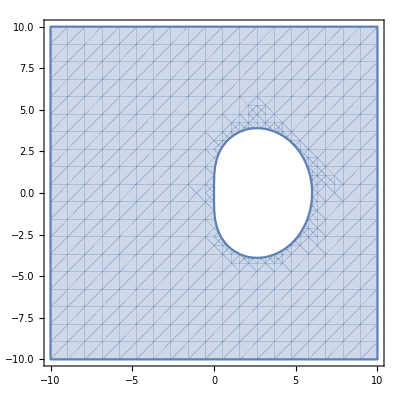

```mathematica
RegionPlot[Abs[GG[x+ⅈ y]]<1,{x,-10,10},{y,-10,10}]
```

```mathematica
(1+z (α1+A012 z (-A021+α1)-A022 (1+z α1)+α2+A021 z α2+A011 (-1+A022 z-z α2)))/(1-z (A022+A012 A021 z)+A011 z (-1+A022 z)) /.{α1->32/41,α2->9/41,c01->23/64,c02->1,c11->0,c12->1,β11->0,β12->1,β21->1,β22->-1,A011->1,A012->-41/64,A021->32/41,A022->9/41,B011->5/8,B012->0,B021->0,B022->7/3}
```

(1+(-9/41 (1+(32 z)/41)+(288 z)/1681) z)/(1-(9/41-z/2) z+(-1+(9 z)/41) z)

```mathematica
GG[z_]:=(1+(-9/41 (1+(32 z)/41)+(288 z)/1681) z)/(1-(9/41-z/2) z+(-1+(9 z)/41) z)
GGKenCarp[z_]:=-((2027836641118 (205372066468156589786682646862506005393283957671868081607098129634478034697432259737245152+z (-63172358211281746707151262345751745284607570169718188421714692711306385685801612264524032+z (-48808867189842884167640045981405766425900613210232968394498532488791459801764750086274170+83488993241781845101431048125584968472179772276029318992788503 z))))/(6242886710420635959355167587673092345451645772368478640901182031 (-4055673282236+1767732205903 z)^3))
```

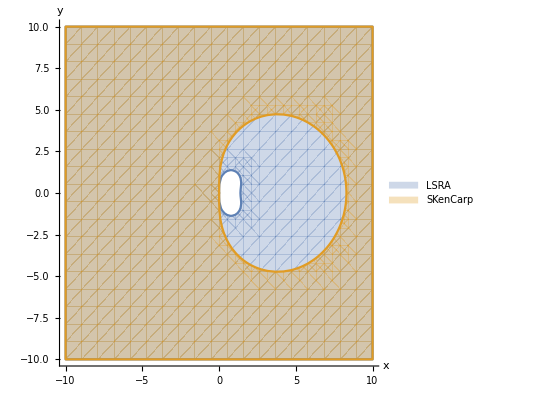

```mathematica
SetOptions[RegionPlot,BaseStyle->{FontFamily->"Ariel",FontSize->22}];
RegionPlot[{Abs[GG[x+ⅈ y]]<1,Abs[GGKenCarp[x+ⅈ y]]<1},{x,-10,10},{y,-10,10},AxesLabel->Automatic,Axes->True,Frame->None,PlotLegends->{Style[LSRA,22],Style[SKenCarp,22]}]
```

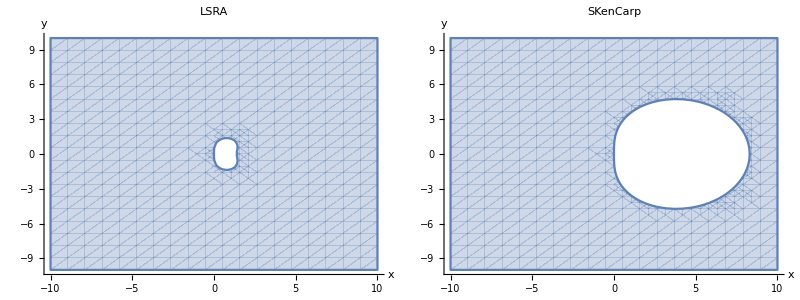

```mathematica
SetOptions[RegionPlot,BaseStyle->{FontFamily->"LM Roman 12",FontSize->22}];
p1 = RegionPlot[{Abs[GG[x+ⅈ y]]<1},{x,-10,10},{y,-10,10},AxesLabel->Automatic,Axes->True,Frame->None,PlotLabel->Style[LSRA,22,FontFamily->"LM Roman 12"],ImageSize->Medium];
p2 = RegionPlot[{Abs[GGKenCarp[x+ⅈ y]]<1},{x,-10,10},{y,-10,10},AxesLabel->Automatic,Axes->True,Frame->None,PlotLabel->Style[SKenCarp,22,FontFamily->"LM Roman 12"],ImageSize->Medium];
Grid[{{p1,p2}}]
```

```mathematica
Export["ImplicitStability.pdf",%]
```

ImplicitStability.pdf

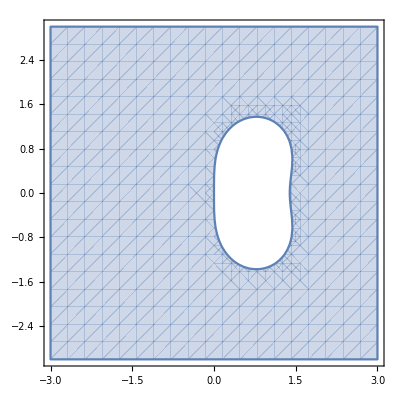

```mathematica
RegionPlot[Abs[GG[x+ⅈ y]]<1,{x,-3,3},{y,-3,3}]
```

```mathematica
(1+z (α1+A012 z (-A021+α1)-A022 (1+z α1)+α2+A021 z α2+A011 (-1+A022 z-z α2)))/(1-z (A022+A012 A021 z)+A011 z (-1+A022 z)) /.{α1->1/3,α2->2/3,c01->0,c02->3/4,c11->0,c12->1,β11->0,β12->1,β21->1,β22->-1,A011->-1,A012->1,A021->0,A022->3/4,B011->2,B012->0,B021->0,B022->1/2}
```

(1+(2-3/4 (1+z/3)+z/4) z)/(1-(3 z)/4-(-1+(3 z)/4) z)

```mathematica
GG2[z_]:=(1+(2-3/4 (1+z/3)+z/4) z)/(1-(3 z)/4-(-1+(3 z)/4) z)
```

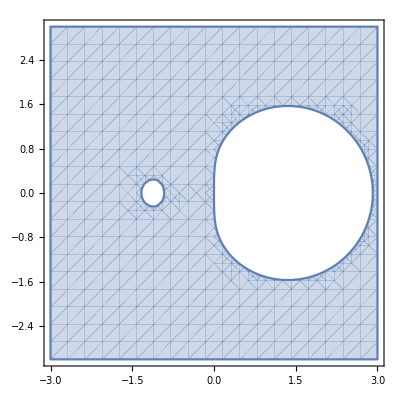

```mathematica
RegionPlot[Abs[GG2[x+ⅈ y]]<1,{x,-3,3},{y,-3,3}]
```

```mathematica
(1+z (α1+A012 z (-A021+α1)-A022 (1+z α1)+α2+A021 z α2+A011 (-1+A022 z-z α2)))/(1-z (A022+A012 A021 z)+A011 z (-1+A022 z)) /.{α1->1/3,α2->2/3,c01->1/4,c02->5/8,c11->0,c12->-1,β11->2,β12->-1,β21->-1,β22->1,A011->-5/8,A012->7/8,A021->-7/48,A022->37/48,B011->0,B012->0,B021->0,B022->3/2}
```

(1+(1-5/8 (-1+(5 z)/48)-37/48 (1+z/3)+(371 z)/1152) z)/(1-(37/48-(49 z)/384) z-5/8 (-1+(37 z)/48) z)

```mathematica
GG3[z_]:=(1+(2-3/4 (1+z/3)+z/4) z)/(1-(3 z)/4-(-1+(3 z)/4) z)
```

```mathematica
RegionPlot[Abs[GG2[x+ⅈ y]]<1,{x,-3,3},{y,-3,3}]
```

-Graphics-